| R | C | L
H(s) | (C R s)/(1+C R s+C L s^2) | 1/(1+C R s+C L s^2) | (C L s^2)/(1+C R s+C L s^2)
H(ω) | (ⅈ C R ω)/(1+ⅈ C R ω-C L ω^2) | 1/(1+ⅈ C R ω-C L ω^2) | -(C L ω^2)/(1+ⅈ C R ω-C L ω^2)

Filter Information:

| 1 | 2
Poles | -0.5-0.866025 ⅈ | -0.5+0.866025 ⅈ
Zeroes | 0. | 0

The Circuit Is A Bandpass Filter Centered At Angular Frequency 1

Bode Plot H(ω)_R:

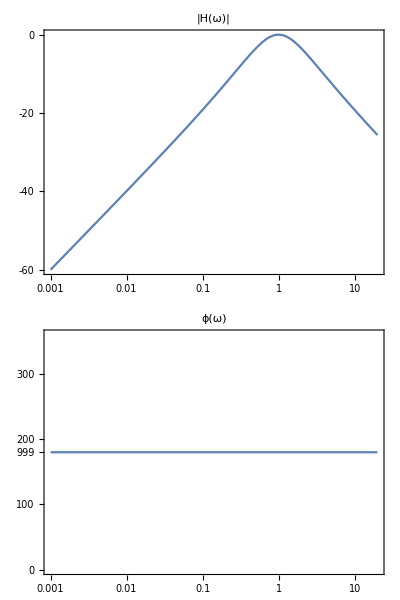

```mathematica
(*Transfer Functions for a simple RCL series circuit*)
(*There are three transfer functions for this circuit depending on which component Subscript[V, 0] is taken across*)

ZR = R;(*Input["Enter The Value Of Resistance:"]*)
ZC = 1/(s C);(*Input["Enter The Value Of Capacitance:"]*)
ZL=s L;(*Input["Enter The Value Of Inductance:"]*)

HS1 = Simplify[ZR/(ZR + ZC +ZL)]//ExpandAll;(*Resistor Voltage*)
HS2 = Simplify[ZC/(ZR + ZC+ ZL)]//ExpandAll;(*Cap Voltage*)
HS3 = Simplify[ZL/(ZR+ZC+ZL)]//ExpandAll;(*Inductor Voltage*)
Hω1 = HS1/.s->ⅉ ω;
Hω2=HS2/.s->ⅉ ω;
Hω3 = HS3 /.s->ⅉ ω;

testParameters={R->1,C->1,L->1};
TableForm[{{HS1,HS2,HS3},{Hω1,Hω2,Hω3}}, TableHeadings->{{"H(s)","H(ω)"},{"R","C","L"}},TableAlignments->{Center, Center}]
StringTemplate["Filter Information: "][]
eqn1=Denominator[HS1]==0;
eqn2 = Numerator[HS1]==0;
pole1 = s/.Solve[eqn1/.testParameters,s][[1]]//N;
pole2 = s/.Solve[eqn1/.testParameters,s][[2]]//N;
zero1 = s/.Solve[eqn2/.testParameters,s][[1]]//N;
zero2 = 0; 
(*zero2 = s/.Solve[eqn2/.testParameters,s][[2]]//N;*)
(*If filter has a second zero, uncomment this line and comment the previous line*)
wc=1/(√(L C))/.testParameters;
flag1=Limit[Abs[Hω1]/.testParameters,ω->0];
flag2 =Limit[Abs[Hω1]/.testParameters,ω->∞];
flag3 =Limit[Abs[Hω1]/.testParameters,ω->wc];
TableForm[{{pole1,pole2},{zero1,zero2}},TableHeadings->{{"Poles","Zeroes"},{"1","2"}}]
If[flag1==1&&flag2==0 &&flag3 ==0,output=StringForm["The Circuit Is a Low-Pass Filter Centered At Angular Frequency ``",wc], If[flag2 ==1 && flag1 == 0 && flag3 ==0, output=StringForm["The Circuit Is A High-Pass Circuit Centered At Angular Frequency ``", wc], output=StringForm["The Circuit Is A Bandpass Filter Centered At Angular Frequency `` ", wc]]];
Style[output,Purple,16]
StringTemplate["Bode Plot H(ω)_R:"][]
BodePlot[Hω1/.testParameters,PlotLabel->{"|H(ω)|","ϕ(ω)"}]
```